# Non-local QFT: field redefinition

```mathematica
$Assumptions=And[g∈Reals,g≠0,ϕ[t]≠0];
```

```mathematica
path=NotebookDirectory[];
```

## d = 1

### Action

Smeared field, truncated to order M.

```mathematica
M=7;
```

```mathematica
ϕs=∑_(p=0)^M (-1)^p/(p!)a^(2p)Derivative[2p][ϕ][t]
(*ϕs=∑_(p=0)^M c[p] a^(2p)ϕ^(2p)[t]*)
```

ϕ[t]-a^2 ϕ''[t]+1/2 a^4 ϕ^(4)[t]-1/6 a^6 ϕ^(6)[t]+1/24 a^8 ϕ^(8)[t]-1/120 a^10 ϕ^(10)[t]+1/720 a^12 ϕ^(12)[t]-(a^14 ϕ^(14)[t])/5040

Action

```mathematica
k=3;
K=-1/2 ϕ[t] ϕ''[t]-1/2 m^2 ϕ[t]^2;
V=1/k ϕs^k;
Sϕ=K+V
```

-1/2 m^2 ϕ[t]^2-1/2 ϕ[t] ϕ''[t]+1/3 (ϕ[t]-a^2 ϕ''[t]+1/2 a^4 ϕ^(4)[t]-1/6 a^6 ϕ^(6)[t]+1/24 a^8 ϕ^(8)[t]-1/120 a^10 ϕ^(10)[t]+1/720 a^12 ϕ^(12)[t]-(a^14 ϕ^(14)[t])/5040)^3

```mathematica
Sϕexp=CoefficientList[Sϕ,a^2,M+1]//Simplify//Expand
```

{-1/2 m^2 ϕ[t]^2+ϕ[t]^3/3-1/2 ϕ[t] ϕ''[t],-ϕ[t]^2 ϕ''[t],ϕ[t] ϕ''[t]^2+1/2 ϕ[t]^2 ϕ^(4)[t],-1/3 ϕ''[t]^3-ϕ[t] ϕ''[t] ϕ^(4)[t]-1/6 ϕ[t]^2 ϕ^(6)[t],1/2 ϕ''[t]^2 ϕ^(4)[t]+1/4 ϕ[t] (ϕ^(4)[t])^2+1/3 ϕ[t] ϕ''[t] ϕ^(6)[t]+1/24 ϕ[t]^2 ϕ^(8)[t],-1/4 ϕ''[t] (ϕ^(4)[t])^2-1/6 ϕ''[t]^2 ϕ^(6)[t]-1/6 ϕ[t] ϕ^(4)[t] ϕ^(6)[t]-1/12 ϕ[t] ϕ''[t] ϕ^(8)[t]-1/120 ϕ[t]^2 ϕ^(10)[t],1/24 (ϕ^(4)[t])^3+1/6 ϕ''[t] ϕ^(4)[t] ϕ^(6)[t]+1/36 ϕ[t] (ϕ^(6)[t])^2+1/24 ϕ''[t]^2 ϕ^(8)[t]+1/24 ϕ[t] ϕ^(4)[t] ϕ^(8)[t]+1/60 ϕ[t] ϕ''[t] ϕ^(10)[t]+1/720 ϕ[t]^2 ϕ^(12)[t],-1/24 (ϕ^(4)[t])^2 ϕ^(6)[t]-1/36 ϕ''[t] (ϕ^(6)[t])^2-1/24 ϕ''[t] ϕ^(4)[t] ϕ^(8)[t]-1/72 ϕ[t] ϕ^(6)[t] ϕ^(8)[t]-1/120 ϕ''[t]^2 ϕ^(10)[t]-1/120 ϕ[t] ϕ^(4)[t] ϕ^(10)[t]-1/360 ϕ[t] ϕ''[t] ϕ^(12)[t]-(ϕ[t]^2 ϕ^(14)[t])/5040}

### Field redefinition

Add total derivative terms to the action.

```mathematica
totalDeriv=Sum[(∑_(l=0)^M c[p,n,2l] a^(2l)m^(2l))a^(2n+n p+1-6)D[((Derivative[p][ϕ][t])^n), t],{p,1,⌊(2 M-1)/3⌋,2},{n,3,⌊(2 M+5)/3⌋,2}]+O[a]^(2(M+1))//Normal;
totalDeriv=totalDeriv/.{c[3,__]->0,c[5,__]->0,c_[1,a_,b_]->c[a,b]};
Collect[totalDeriv,a^2]
```

3 a^4 c[3,0] ϕ'[t]^2 ϕ''[t]+3 a^6 m^2 c[3,2] ϕ'[t]^2 ϕ''[t]+3 a^8 m^4 c[3,4] ϕ'[t]^2 ϕ''[t]+a^10 (3 m^6 c[3,6] ϕ'[t]^2 ϕ''[t]+5 c[5,0] ϕ'[t]^4 ϕ''[t])+a^12 (3 m^8 c[3,8] ϕ'[t]^2 ϕ''[t]+5 m^2 c[5,2] ϕ'[t]^4 ϕ''[t])+a^14 (3 m^10 c[3,10] ϕ'[t]^2 ϕ''[t]+5 m^4 c[5,4] ϕ'[t]^4 ϕ''[t])

Field redefinition: ϕ→ϕ+δϕ.

```mathematica
ϕRedefRep={ϕ->Function[t,ϕ[t]+δϕ[t]]}
```

{ϕ→Function[t,ϕ[t]+δϕ[t]]}

```mathematica
Kr=(K/.ϕRedefRep//Expand)/.{δϕ''[t]X__[t_] :>δϕ[t] D[X[t], t,t]}
Vr=V/.ϕRedefRep;
Sr=Kr+Vr
```

-1/2 m^2 δϕ[t]^2-m^2 δϕ[t] ϕ[t]-1/2 m^2 ϕ[t]^2-1/2 δϕ[t] δϕ''[t]-δϕ[t] ϕ''[t]-1/2 ϕ[t] ϕ''[t]

-1/2 m^2 δϕ[t]^2-m^2 δϕ[t] ϕ[t]-1/2 m^2 ϕ[t]^2-1/2 δϕ[t] δϕ''[t]-δϕ[t] ϕ''[t]-1/2 ϕ[t] ϕ''[t]+1/3 (δϕ[t]+ϕ[t]-a^2 (δϕ''[t]+ϕ''[t])+1/2 a^4 (δϕ^(4)[t]+ϕ^(4)[t])-1/6 a^6 (δϕ^(6)[t]+ϕ^(6)[t])+1/24 a^8 (δϕ^(8)[t]+ϕ^(8)[t])-1/120 a^10 (δϕ^(10)[t]+ϕ^(10)[t])+1/720 a^12 (δϕ^(12)[t]+ϕ^(12)[t])-(a^14 (δϕ^(14)[t]+ϕ^(14)[t]))/5040)^3

Expand the field redefinition in powers of a^2.

```mathematica
δϕExpRep={δϕ->Function[t,∑_(p=1)^M a^(2p)δϕ[2p][t]]}
```

{δϕ→Function[t,∑_(p=1)^M a^(2 p) δϕ[2 p][t]]}

Action with expanded field redefinition and total derivatives.

```mathematica
Sϕexp=CoefficientList[totalDeriv+(Sr//Expand)/.δϕExpRep,a^2,M+1]//Simplify//Expand;
```

### Cancelling higher-derivatives

#### Tools

Find all derivative orders appearing in an expression.

```mathematica
findOrders[expr_]:=Cases[expr//Expand,Derivative[ord_][ϕ_][t]:>{ord},∞];
```

Find the necessary field redefinition for at order 2p, i.e. the terms to have in δϕ[2p], to cancel term multiplied by ϕ''. Note that it does not perform any integration by part. One has to use other functions for this.

```mathematica
findQuadRedef[p_,expr_]:=Module[{dblcoll,factor,sol},
dblcoll=CoefficientList[expr//Expand,ϕ''[t]][[2;;-1]];
factor=dblcoll.Table[ϕ''[t]^n,{n,0,Length[dblcoll]-1}];
sol=Solve[factor==0,δϕ[2(p-1)][t]]//Simplify//Flatten
];
```

This function cancels any term in front of ϕ''[t] by a term in the field redefinition and inserts the terms to a table storing field redefinitions. This allows to use them in higher-order terms. The function always reinserts the field variation in order to cancel further terms later, except if there was nothing to cancel.

TODO: return value instead of modifying table (return also field redefinition?)

```mathematica
shiftRedef[p_,expr_]:=Module[{rep,redef},
sol=findQuadRedef[p,expr//Expand];
redef=δϕ[2(p-1)][t]/.sol//Simplify;
rep=sol/.{{δ_->F_}->{δ->F+δ}};
{(expr//Expand)/.rep//Simplify,redef}
];
```

Integrate by part ϕ^(k) to obtain ϕ^(2).

```mathematica
IPPHigherToSecondRep[k_]:={(Derivative[k][ϕ][t])^(n_.)X_:>(-1)^(k-2)Derivative[2][ϕ][t]D[X (Derivative[k][ϕ][t])^(n-1),{t,k-2}]};
```

This computation integrates by part the the lowest-order derivatives of at least order 3 in a given term. To simplify a sum of terms, use Map.

```mathematica
reduceHigherTerms[expr_]:=Module[{orders,minOrder},
orders=findOrders[expr//Expand]//Flatten;
minOrder=Min[Select[orders,#>2&]];
If[minOrder==∞,
expr,
(expr//Expand)/.IPPHigherToSecondRep[minOrder]//Simplify
]
];
```

Integrate by part (∂_t ϕ)^p ϕ^q to obtain (ϕ^(2)(∂_t ϕ))^(p-2)(…).

The expression of the replacement rule is complicated because the simple pattern does not match the case where q=0.

```mathematica
IPPLinToSecondRep={X_.(D[ϕ[t], t])^p_:>(1-p)Derivative[2][ϕ][t](D[ϕ[t], t])^(p-2)If[MatchQ[X,c_ ϕ[t]^(_.)],X/.{ϕ[t]^(q_.):>ϕ[t]^(q+1)/(1+q)},ϕ[t] X]};
```

This computation integrates by part two first-order derivatives in terms containing only first-order derivatives. In this case, Map is not necessary (because all terms have first-order derivatives or no derivatives).

```mathematica
reduceFirstTerms[expr_]:=Module[{orders},
orders=findOrders[expr//Expand]//Flatten;
If[Max[orders]>2||Length[orders]==0,
expr,
(expr//Expand)/.IPPLinToSecondRep//Simplify
]
];
```

Remove recursively high-order derivatives.

```mathematica
shiftRedefRec[p_,expr_]:=Module[{result=expr,redefSum=0,redef},
While[True,
{result,redef}=shiftRedef[p,result//Expand]//Simplify//Expand;
redefSum+=redef;
If[redef===0,Break[]];
];
{result,redefSum}
]
```

```mathematica
reduceRecusively[p_,expr_]:=Module[
{result,redefSum=0,redef,i=0,MaxIter=100},
result=expr;

(*{result,redef}=shiftRedef[p,result//Expand]//Simplify//Expand;*)
{result,redef}=shiftRedefRec[p,result];
redefSum+=redef;

While[Max[findOrders[result//Expand]]>2,
i+=1;
If[i>MaxIter,
Print["MaxIter reached."];
Break[]
];(* avoid infinite loop *)
result=reduceHigherTerms/@(result//Expand);

(*While[True,
{result,redef}=shiftRedef[p,result//Expand]//Simplify//Expand;
redefSum+=redef;
If[redef===0,Break[]];
];*)
{result,redef}=shiftRedefRec[p,result];
redefSum+=redef;
];

(*While[Max[findOrders[result//Expand]]>0,*)
While[findOrders[result//Expand]!={{2}},
i+=1;
If[i>MaxIter,
Print["MaxIter reached."];
Break[]
];(* avoid infinite loop *)

result=reduceFirstTerms[result//Expand]//Simplify//Expand;

(*While[True,
{result,redef}=shiftRedef[p,result//Expand]//Simplify//Expand;
redefSum+=redef;
If[redef===0,Break[]];
];*)
{result,redef}=shiftRedefRec[p,result];
redefSum+=redef;
];

{result/.{δϕ[2(p-1)][t]->0}//Simplify//Expand,redefSum//Simplify//Expand}
];
```

#### Computations

We define a table used to store the terms of the field redefinition at each order.

```mathematica
δϕTable=Table[0,M+1];
SϕNew=Sϕexp;
```

Write the action and field redefinition up to order a^p.

```mathematica
rebuildAction[p_]:=Sum[a^(2i)SϕNew[[i+1]],{i,0,p}]//Expand;
rebuildRedef[p_]:=Sum[a^(2i)δϕTable[[i+1]],{i,0,p}]//Expand;
```

```mathematica
organizeByPower[expr_]:=Collect[expr,{ϕ[t],a^2,m^2}];
rescaleAction[expr_]:=1/m^6 expr/.{ϕ[t]->m^2 ϕ[t],a->α/m}//Simplify;
VrScaled[p_]:=-rescaleAction[rebuildAction[p]]/.{g->1,ϕ[t]->ϕ,ϕ''[t]->0}//Expand//Collect[#,ϕ]&;
```

Get the replacement rule to implement the field redefinition up to order p.

Note: it is not possible to replace δϕTable by an argument: otherwise, Mathematica is not able to build properly the function and derivatives are set to zero.

```mathematica
repRedef[p_]:=Table[
{δϕ[2(n-1)]->Function[t,δϕTable[[n]]//Expand//Evaluate]},
{n,1,p-1}]//Flatten;
```

Perform the field redefinition recursively.

```mathematica
tranformAction[]:=Module[
{},
Do[
Print["Order: ",a^(2(p-1))];
SϕNew[[p]]=(Sϕexp[[p]]//Expand)/.repRedef[p]//Simplify//Expand;
{SϕNew[[p]],δϕTable[[p]]}=reduceRecusively[p,SϕNew[[p]]],
{p,2,M+1}]//Simplify//Expand;
];
```

Simplify the potential using the ambiguities due to total derivatives.

```mathematica
findCanonicalPotential[expr_]:=Module[{redef={},result,elem,var},
result=CoefficientList[expr//rescaleAction,{ϕ[t],α^2}]/.{ϕ''[t]->0}//Flatten;
result=Select[result,Not[NumericQ[#]]&];
result=result//Simplify//Expand;
Do[
var=FirstCase[elem/.redef,X_ c[n__]:>c[n]];
redef = Catenate[{redef,Solve[elem==0/.redef,var]//Flatten}],
{elem,result}];
redef
];
```

Start computations.

```mathematica
SϕNew[[1]]=Sϕexp[[1]]
δϕTable[[1]]+=0;
```

-1/2 m^2 ϕ[t]^2+ϕ[t]^3/3-1/2 ϕ[t] ϕ''[t]

```mathematica
tranformAction[]
```

Order: a^2

Order: a^4

Order: a^6

Order: a^8

Order: a^10

Order: a^12

Order: a^14

```mathematica
p=M;
rebuildRedef[p]//Expand//Collect[#,a^2]&;
```

```mathematica
p=M;
SϕRedef=rebuildAction[p]//Expand//organizeByPower
```

-1/2 m^2 ϕ[t]^2+(1/3+a^2 m^2+a^4 m^4 (3/2-3/2 c[3,0])+a^6 m^6 (2-3/2 c[3,2])+a^8 m^8 (9/4-3/2 c[3,4])+a^10 m^10 (23/10-3/2 c[3,6])+a^12 m^12 (-13/30-3/2 c[3,8])+a^14 m^14 (2747/210-3/2 c[3,10])) ϕ[t]^3+(-a^2+a^4 m^2 (-19/3+5/2 c[3,0])+a^6 m^4 (-419/18+15/2 c[3,0]+5/2 c[3,2])+a^8 m^6 (-4595/72+45/4 c[3,0]-45/8 c[3,0]^2+15/2 c[3,2]+5/2 c[3,4])+a^10 m^8 (-25639/180+15 c[3,0]+45/4 c[3,2]-45/4 c[3,0] c[3,2]+15/2 c[3,4]+5/2 c[3,6])+a^12 m^10 (-287449/1080+135/8 c[3,0]+15 c[3,2]-45/8 c[3,2]^2+45/4 c[3,4]-45/4 c[3,0] c[3,4]+15/2 c[3,6]+5/2 c[3,8])+a^14 m^12 (-1713371/3780+69/4 c[3,0]+135/8 c[3,2]+15 c[3,4]-45/4 c[3,2] c[3,4]+45/4 c[3,6]-45/4 c[3,0] c[3,6]+15/2 c[3,8]+5/2 c[3,10])) ϕ[t]^4+(a^4 (16/3-c[3,0])+a^6 m^2 (517/9-15 c[3,0]-c[3,2])+a^8 m^4 (12331/36-75 c[3,0]+63/4 c[3,0]^2-15 c[3,2]-c[3,4])+a^10 m^6 (108739/72-301 c[3,0]+243/8 c[3,0]^2-75 c[3,2]+63/2 c[3,0] c[3,2]-15 c[3,4]-c[3,6]-15/8 c[5,0])+a^12 m^8 (22887349/4320-35267/32 c[3,0]-3537/32 c[3,0]^2+729/32 c[3,0]^3-301 c[3,2]+243/4 c[3,0] c[3,2]+63/4 c[3,2]^2-75 c[3,4]+63/2 c[3,0] c[3,4]-15 c[3,6]-c[3,8]-15/8 c[5,2])+a^14 m^10 (145895227/30240-43609/8 c[3,0]-378 c[3,0]^2-35267/32 c[3,2]-3537/16 c[3,0] c[3,2]+2187/32 c[3,0]^2 c[3,2]+243/8 c[3,2]^2-301 c[3,4]+243/4 c[3,0] c[3,4]+63/2 c[3,2] c[3,4]-75 c[3,6]+63/2 c[3,0] c[3,6]-15 c[3,8]-c[3,10]-15/8 c[5,4])) ϕ[t]^5+(a^6 (-118/3+7 c[3,0])+a^8 m^2 (-9194/15+364/3 c[3,0]-14 c[3,0]^2+7 c[3,2])+a^10 m^4 (-5684671/1080+9478/9 c[3,0]-861/8 c[3,0]^2+364/3 c[3,2]-28 c[3,0] c[3,2]+7 c[3,4]+35/8 c[5,0])+a^12 m^6 (-2106133111/64800+1788395/288 c[3,0]-3507/32 c[3,0]^2-441/32 c[3,0]^3+9478/9 c[3,2]-861/4 c[3,0] c[3,2]-14 c[3,2]^2+364/3 c[3,4]-28 c[3,0] c[3,4]+7 c[3,6]+105/8 c[5,0]+35/8 c[5,2])+a^14 m^8 (-31229149579/226800+(46762499 c[3,0])/1440-455/32 c[3,0]^2-6993/32 c[3,0]^3+1788395/288 c[3,2]-3507/16 c[3,0] c[3,2]-1323/32 c[3,0]^2 c[3,2]-861/8 c[3,2]^2+9478/9 c[3,4]-861/4 c[3,0] c[3,4]-28 c[3,2] c[3,4]+364/3 c[3,6]-28 c[3,0] c[3,6]+7 c[3,8]+315/16 c[5,0]-315/16 c[3,0] c[5,0]+105/8 c[5,2]+35/8 c[5,4])) ϕ[t]^6+(a^8 (15812/45-164/3 c[3,0]+4 c[3,0]^2)+a^10 m^2 (199094/27-11744/9 c[3,0]+114 c[3,0]^2-164/3 c[3,2]+8 c[3,0] c[3,2]-10/3 c[5,0])+a^12 m^4 (339854411/4050-1305023/90 c[3,0]+1929/2 c[3,0]^2-105/2 c[3,0]^3-11744/9 c[3,2]+228 c[3,0] c[3,2]+4 c[3,2]^2-164/3 c[3,4]+8 c[3,0] c[3,4]-35 c[5,0]-10/3 c[5,2])+a^14 m^6 (38200368023/56700-19974197/180 c[3,0]+25911/4 c[3,0]^2+1035/4 c[3,0]^3-1305023/90 c[3,2]+1929 c[3,0] c[3,2]-315/2 c[3,0]^2 c[3,2]+114 c[3,2]^2-11744/9 c[3,4]+228 c[3,0] c[3,4]+8 c[3,2] c[3,4]-164/3 c[3,6]+8 c[3,0] c[3,6]-155 c[5,0]+135/2 c[3,0] c[5,0]-35 c[5,2]-10/3 c[5,4])) ϕ[t]^7+(a^10 (-324791/90+1564/3 c[3,0]-75/2 c[3,0]^2+5/6 c[5,0])+a^12 m^2 (-146246011/1512+355885/24 c[3,0]-9015/8 c[3,0]^2+495/8 c[3,0]^3+1564/3 c[3,2]-75 c[3,0] c[3,2]+30 c[5,0]+5/6 c[5,2])+a^14 m^4 (-371806511287/264600+4943089/24 c[3,0]-65105/4 c[3,0]^2+2835/8 c[3,0]^3+355885/24 c[3,2]-9015/4 c[3,0] c[3,2]+1485/8 c[3,0]^2 c[3,2]-75/2 c[3,2]^2+1564/3 c[3,4]-75 c[3,0] c[3,4]+1335/4 c[5,0]-675/8 c[3,0] c[5,0]+30 c[5,2]+5/6 c[5,4])) ϕ[t]^8+(a^12 (23358229/567-48184/9 c[3,0]+1150/3 c[3,0]^2-55/3 c[3,0]^3-25/3 c[5,0])+a^14 m^2 (21792856501/15876-19781351/108 c[3,0]+527365/36 c[3,0]^2-2365/4 c[3,0]^3-48184/9 c[3,2]+2300/3 c[3,0] c[3,2]-55 c[3,0]^2 c[3,2]-4925/18 c[5,0]+275/6 c[3,0] c[5,0]-25/3 c[5,2])) ϕ[t]^9+a^14 (-4865638327/9450+603537/10 c[3,0]-26851/6 c[3,0]^2+407/2 c[3,0]^3+1375/18 c[5,0]-55/6 c[3,0] c[5,0]) ϕ[t]^10-1/2 ϕ[t] ϕ''[t]

```mathematica
canRedef=findCanonicalPotential[SϕRedef]//Expand
SϕRedef/.canRedef//Simplify//Expand//organizeByPower
```

{c[3,0]→1,c[3,2]→4/3,c[3,4]→3/2,c[3,6]→23/15,c[3,8]→-13/45,c[3,10]→2747/315,c[5,0]→416738/675,c[5,2]→4026088/2025,c[5,4]→-90480893/56700}

-1/2 m^2 ϕ[t]^2+(1/3+a^2 m^2) ϕ[t]^3+(-a^2-(23 a^4 m^2)/6-(112 a^6 m^4)/9-(400 a^8 m^6)/9-(5056 a^10 m^8)/45-(30848 a^12 m^10)/135-(372224 a^14 m^12)/945) ϕ[t]^4+((13 a^4)/3+(370 a^6 m^2)/9+(2356 a^8 m^4)/9) ϕ[t]^5+(-(97 a^6)/3-(7444 a^8 m^2)/15-(40016 a^10 m^4)/27-(16951588 a^12 m^6)/2025-(365040328 a^14 m^8)/4725) ϕ[t]^6+((13532 a^8)/45+(1645424 a^10 m^2)/405+(246594764 a^12 m^4)/6075+(18403444376 a^14 m^6)/42525) ϕ[t]^7+(-(1057238 a^10)/405-(528895198 a^12 m^2)/8505-(293278365536 a^14 m^4)/297675) ϕ[t]^8+((17612426 a^12)/567+(1376189404 a^14 m^2)/1323) ϕ[t]^9-(17745598574 a^14 ϕ[t]^10)/42525-1/2 ϕ[t] ϕ''[t]

```mathematica
VrScaledCan[p]=VrScaled[p]/.canRedef//Simplify//Collect[#,{ϕ,α}]&
```

ϕ^2/2+(-1/3-α^2) ϕ^3+(α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45+(30848 α^12)/135+(372224 α^14)/945) ϕ^4+(-(13 α^4)/3-(370 α^6)/9-(2356 α^8)/9) ϕ^5+((97 α^6)/3+(7444 α^8)/15+(40016 α^10)/27+(16951588 α^12)/2025+(365040328 α^14)/4725) ϕ^6+(-(13532 α^8)/45-(1645424 α^10)/405-(246594764 α^12)/6075-(18403444376 α^14)/42525) ϕ^7+((1057238 α^10)/405+(528895198 α^12)/8505+(293278365536 α^14)/297675) ϕ^8+(-(17612426 α^12)/567-(1376189404 α^14)/1323) ϕ^9+(17745598574 α^14 ϕ^10)/42525

```mathematica
(* save result for comparison *)
ϕ^2/2+(-1/3-α^2) ϕ^3+(α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45) ϕ^4+(-(13 α^4)/3-(370 α^6)/9-(2356 α^8)/9) ϕ^5+((97 α^6)/3+(7444 α^8)/15+(40016 α^10)/27) ϕ^6+(-(13532 α^8)/45-(1645424 α^10)/405) ϕ^7+(1057238 α^10 ϕ^8)/405
```

ϕ^2/2+(-1/3-α^2) ϕ^3+(α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45) ϕ^4+(-(13 α^4)/3-(370 α^6)/9-(2356 α^8)/9) ϕ^5+((97 α^6)/3+(7444 α^8)/15+(40016 α^10)/27) ϕ^6+(-(13532 α^8)/45-(1645424 α^10)/405) ϕ^7+(1057238 α^10 ϕ^8)/405

```mathematica
VrScaledTab=Table[VrScaledCan[p],{p,1,M}]/.ϕ'[t]->0//Simplify;
```

```mathematica
Manipulate[Plot[VrScaledTab[[p]]/.{α->αp,p->pp},{ϕ,-ϕl,ϕl}],{{αp,0.01,α},0.01,0.5},{{pp,2,"p"},1,M,1},{{ϕl,0.1,"ϕ_max"},0.1,2000}]
```

Part::partd: Part specification VrScaledTab⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification VrScaledTab⟦11⟧ is longer than depth of object.

Part::partd: Part specification VrScaledTab⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

### Convergence of coefficients

```mathematica
Vpot=VrScaledCan[p];
```

```mathematica
p=11;
Vpot=(m^2 ϕ^2)/2+(-1/3-a^2 m^2) ϕ^3+(a^2+(23 a^4 m^2)/6+(112 a^6 m^4)/9+(400 a^8 m^6)/9+(5056 a^10 m^8)/45+(30848 a^12 m^10)/135+(372224 a^14 m^12)/945+(111872 a^16 m^14)/189+(959488 a^18 m^16)/1215+(40306688 a^20 m^18)/42525+(483713024 a^22 m^20)/467775) ϕ^4+(-(13 a^4)/3-(370 a^6 m^2)/9-(2356 a^8 m^4)/9) ϕ^5+((97 a^6)/3+(7444 a^8 m^2)/15+(40016 a^10 m^4)/27+(16951588 a^12 m^6)/2025+(365040328 a^14 m^8)/4725+(704360354 a^16 m^10)/1575+(53044107164 a^18 m^12)/25515+(5345363837636 a^20 m^14)/637875+(212689374482008 a^22 m^16)/7016625) ϕ^6+(-(13532 a^8)/45-(1645424 a^10 m^2)/405-(246594764 a^12 m^4)/6075-(18403444376 a^14 m^6)/42525) ϕ^7+((1057238 a^10)/405+(528895198 a^12 m^2)/8505+(293278365536 a^14 m^4)/297675+(330220197478 a^16 m^6)/297675+(4539699316064 a^18 m^8)/535815+(3762791962092662 a^20 m^10)/13395375+(18508000088422676 a^22 m^12)/5893965) ϕ^8+(-(17612426 a^12)/567-(1376189404 a^14 m^2)/1323-(1461162201244 a^16 m^4)/178605-(152243548796524 a^18 m^6)/1607445-(14516307774038468 a^20 m^8)/8037225) ϕ^9+((17745598574 a^14)/42525+(91967935202338 a^16 m^2)/8037225+(3255947000654108 a^18 m^4)/14467005+(339406560100146388 a^20 m^6)/72335025-(36650456262120146896 a^22 m^8)/3978426375) ϕ^10+(-(5599006958392 a^16)/1148175-(2226671149812904 a^18 m^2)/10333575-(461350316377218328 a^20 m^4)/72335025-(13262953310597307088 a^22 m^6)/795685275) ϕ^11+((604370472837748 a^18)/8037225+(3570960644823919238 a^20 m^2)/795685275+(107753866659559323248 a^22 m^4)/1705039875) ϕ^12+(-(1954323884798776 a^20)/1515591-(60074374172932678156 a^22 m^2)/1023023925) ϕ^13+(11898606015180066008 a^22 ϕ^14)/651015225/.{a->α,m->1};
```

#### In ξ^2

```mathematica
ξ2Table=Table[i,{i,2,2p,2}]
```

{2,4,6,8,10,12,14,16,18,20,22}

α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45+(30848 α^12)/135+(372224 α^14)/945+(111872 α^16)/189+(959488 α^18)/1215+(40306688 α^20)/42525+(483713024 α^22)/467775

{1,23/6,112/9,400/9,5056/45,30848/135,372224/945,111872/189,959488/1215,40306688/42525,483713024/467775}

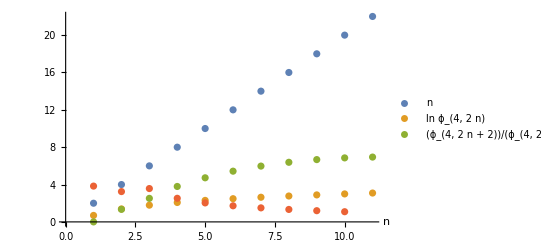

```mathematica
Vϕ4=Coefficient[Vpot,ϕ^4]
Vϕ4Coeff=CoefficientList[Vϕ4,α^2][[2;;p+1]]
Vϕ4CoeffRatio=Table[Vϕ4Coeff[[i+1]]/Vϕ4Coeff[[i]],{i,1,p-1}];
DiscretePlot[{ξ2Table[[i]],Log[ξ2Table[[i]]],Log[Vϕ4Coeff][[i]],Vϕ4CoeffRatio[[i]]},{i,1,p},
Filling->None,PlotLegends->Placed[{"n","ln ϕ_(4, 2  n)","(ϕ_(4, 2  n + 2))/(ϕ_(4, 2  n))"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}]
Export[path<>"coeff_phi4_xi2.pdf",%];
```

(97 α^6)/3+(7444 α^8)/15+(40016 α^10)/27+(16951588 α^12)/2025+(365040328 α^14)/4725+(704360354 α^16)/1575+(53044107164 α^18)/25515+(5345363837636 α^20)/637875+(212689374482008 α^22)/7016625

{97/3,7444/15,40016/27,16951588/2025,365040328/4725,704360354/1575,53044107164/25515,5345363837636/637875,212689374482008/7016625}

{7444/485,50020/16749,4237897/750300,273780246/29665279,1056540531/182520164,132610267910/28526594337,1336340959409/331525669775,53172343620502/14699750553499}

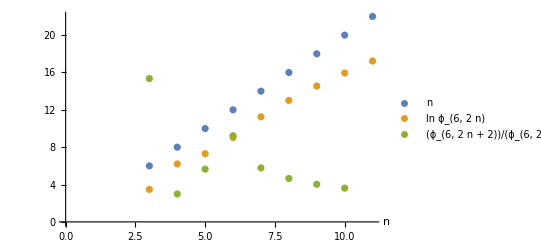

```mathematica
Vϕ6=Coefficient[Vpot,ϕ^6]
Vϕ6Coeff=CoefficientList[Vϕ6,α^2][[4;;p+1]]
Vϕ6CoeffRatio=Table[Vϕ6Coeff[[i+1]]/Vϕ6Coeff[[i]],{i,1,p-3}]
DiscretePlot[{ξ2Table[[i]],Log[Vϕ6Coeff][[i-2]],Vϕ6CoeffRatio[[i-2]]},{i,3,p},Filling->None,PlotLegends->Placed[{"n","ln ϕ_(6, 2  n)","(ϕ_(6, 2  n + 2))/(ϕ_(6, 2  n))"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}]
Export[path<>"coeff_phi6_xi2.pdf",%];
```

(1057238 α^10)/405+(528895198 α^12)/8505+(293278365536 α^14)/297675+(330220197478 α^16)/297675+(4539699316064 α^18)/535815+(3762791962092662 α^20)/13395375+(18508000088422676 α^22)/5893965

{0,1057238/405,528895198/8505,293278365536/297675,330220197478/297675,4539699316064/535815,3762791962092662/13395375,18508000088422676/5893965}

{1057238/13095,264447599/2110374,18329897846/27573525,165110098739/1245941718,2837312072540/25872233247,1881395981046331/2995292405385,4627000022105669/3063297188721}

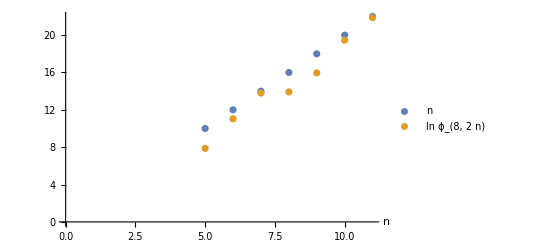

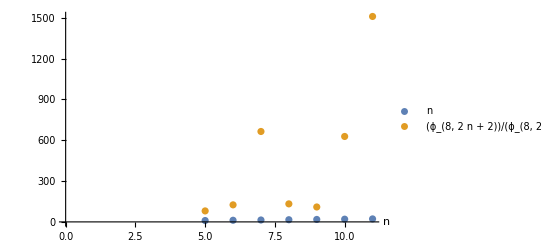

```mathematica
Vϕ8=Coefficient[Vpot,ϕ^8]
Vϕ8Coeff=CoefficientList[Vϕ8,α^2][[5;;p+1]]
Vϕ8CoeffRatio=Table[Vϕ8Coeff[[i+1]]/Vϕ6Coeff[[i]],{i,1,p-4}]
DiscretePlot[{ξ2Table[[i]],Log[Vϕ8Coeff][[i-3]]},{i,5,p},Filling->None,PlotLegends->Placed[{"n","ln ϕ_(8, 2  n)"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}]
Export[path<>"coeff_phi8_xi2_log.pdf",%];
DiscretePlot[{ξ2Table[[i]],Vϕ8CoeffRatio[[i-4]]},{i,5,p},Filling->None,PlotLegends->Placed[{"n","(ϕ_(8, 2  n + 2))/(ϕ_(8, 2  n))"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}]
Export[path<>"coeff_phi8_xi2_ratio.pdf",%];
```

#### In ϕ

```mathematica
VϕCoeff=CoefficientList[Vpot,ϕ][[3;;]]
VϕCoeffRatio=Table[VϕCoeff[[i+1]]/VϕCoeff[[i]],{i,1,8}]//Simplify
```

{1/2,-1/3-α^2,α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45+(30848 α^12)/135+(372224 α^14)/945+(111872 α^16)/189+(959488 α^18)/1215+(40306688 α^20)/42525+(483713024 α^22)/467775,-(13 α^4)/3-(370 α^6)/9-(2356 α^8)/9,(97 α^6)/3+(7444 α^8)/15+(40016 α^10)/27+(16951588 α^12)/2025+(365040328 α^14)/4725+(704360354 α^16)/1575+(53044107164 α^18)/25515+(5345363837636 α^20)/637875+(212689374482008 α^22)/7016625,-(13532 α^8)/45-(1645424 α^10)/405-(246594764 α^12)/6075-(18403444376 α^14)/42525,(1057238 α^10)/405+(528895198 α^12)/8505+(293278365536 α^14)/297675+(330220197478 α^16)/297675+(4539699316064 α^18)/535815+(3762791962092662 α^20)/13395375+(18508000088422676 α^22)/5893965,-(17612426 α^12)/567-(1376189404 α^14)/1323-(1461162201244 α^16)/178605-(152243548796524 α^18)/1607445-(14516307774038468 α^20)/8037225,(17745598574 α^14)/42525+(91967935202338 α^16)/8037225+(3255947000654108 α^18)/14467005+(339406560100146388 α^20)/72335025-(36650456262120146896 α^22)/3978426375,-(5599006958392 α^16)/1148175-(2226671149812904 α^18)/10333575-(461350316377218328 α^20)/72335025-(13262953310597307088 α^22)/795685275,(604370472837748 α^18)/8037225+(3570960644823919238 α^20)/795685275+(107753866659559323248 α^22)/1705039875,-(1954323884798776 α^20)/1515591-(60074374172932678156 α^22)/1023023925,(11898606015180066008 α^22)/651015225}

{-2/3-2 α^2,-(3 (α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45+(30848 α^12)/135+(372224 α^14)/945+(111872 α^16)/189+(959488 α^18)/1215+(40306688 α^20)/42525+(483713024 α^22)/467775))/(1+3 α^2),-(103950 α^2 (39+370 α^2+2356 α^4))/(935550+3586275 α^2+11642400 α^4+41580000 α^6+105114240 α^8+213776640 α^10+368501760 α^12+553766400 α^14+738805760 α^16+886747136 α^18+967426048 α^20),-(α^2 (226870875+3482117100 α^2+10399158000 α^4+58737252420 α^6+542084887080 α^8+3137925377070 α^10+14587129470100 α^12+58799002213996 α^14+212689374482008 α^16))/(779625 (39+370 α^2+2356 α^4)),-(660 α^2 (3196935+43192380 α^2+431540837 α^4+4600861094 α^6))/(226870875+3482117100 α^2+10399158000 α^4+58737252420 α^6+542084887080 α^8+3137925377070 α^10+14587129470100 α^12+58799002213996 α^14+212689374482008 α^16),-(α^2 (192324807675+4581554652675 α^2+72586395470160 α^4+81729498875805 α^6+624208655958800 α^8+20695355791509641 α^10+231350001105283450 α^12))/(6930 (3196935+43192380 α^2+431540837 α^4+4600861094 α^6)),-(55 α^2 (124828069275+4180175314650 α^2+32876149527990 α^4+380608871991310 α^6+7258153887019234 α^8))/(3 (192324807675+4581554652675 α^2+72586395470160 α^4+81729498875805 α^6+624208655958800 α^8+20695355791509641 α^10+231350001105283450 α^12)),(α^2 (-830094737295285-22762063962578655 α^2-447692712589939850 α^4-9333680402754025670 α^6+18325228131060073448 α^8))/(495 (124828069275+4180175314650 α^2+32876149527990 α^4+380608871991310 α^6+7258153887019234 α^8))}

```mathematica
plotVCoeff[αp_]:=Module[{g1,g2},
g1=DiscretePlot[{i,Abs[VϕCoeffRatio[[i-2]]]/.α->αp},{i,3,15},Filling->None,PlotLegends->Placed[{"n","|(ϕ_(n + 1))/ϕ_n|"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}];
Export[path<>"coeff_phi_ratio_xi="<>ToString[αp]<>".pdf",Show[g1,PlotRange->Full]];
g2=DiscretePlot[{i,Log[Abs[VϕCoeff[[i-2]]]]/.α->αp},{i,3,14},Filling->None,PlotLegends->Placed[{"n","ln |ϕ_n|"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}];
Export[path<>"coeff_phi_log_xi="<>ToString[αp]<>".pdf",g2];
GraphicsRow[{Show[g1,PlotRange->Full],Show[g2,PlotRange->Full]}]
];
plotVCoeff[0.3]
plotVCoeff[0.6]
plotVCoeff[1.1]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Manipulate[
Show[DiscretePlot[{i,Abs[VϕCoeffRatio[[i-2]]]/.α->αp},{i,3,8},Filling->None,PlotLegends->Placed[{"ϕ^n","(ϕ_(n + 1))/ϕ_n"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}],PlotRange->Full],
{αp,0.01,1,0.05}]
```

### Study of total derivatives

```mathematica
redefPart=(ϕ[t]^2-m^2 ϕ[t]) δϕ[0][t]-δϕ[0][t] ϕ''[t];
```

```mathematica
D[((Derivative[1][ϕ][t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
%%[[2]];
```

-3/2 m^4 ϕ[t]^3+5/2 m^2 ϕ[t]^4-ϕ[t]^5

```mathematica
D[((Derivative[1][ϕ][t])^5), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

-15/8 m^6 ϕ[t]^5+35/8 m^4 ϕ[t]^6-10/3 m^2 ϕ[t]^7+(5 ϕ[t]^8)/6

```mathematica
D[((Derivative[1][ϕ][t])^7), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

-35/16 m^8 ϕ[t]^7+105/16 m^6 ϕ[t]^8-175/24 m^4 ϕ[t]^9+385/108 m^2 ϕ[t]^10-(35 ϕ[t]^11)/54

```mathematica
D[((Derivative[3][ϕ][t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

-3 m^10 ϕ[t]^3+5 m^8 ϕ[t]^4-2 m^6 ϕ[t]^5

```mathematica
D[(Derivative[1][ϕ][t]Derivative[2][ϕ][t]), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0

```mathematica
D[((Derivative[1][ϕ][t])^3 Derivative[2][ϕ][t]), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0

```mathematica
D[((Derivative[1][ϕ][t])^3(Derivative[2][ϕ][t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0

```mathematica
D[((Derivative[1][ϕ][t])^2 Derivative[2][ϕ][t]Derivative[3][ϕ][t]), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0

```mathematica
D[(Derivative[1][ϕ][t](Derivative[3][ϕ][t])^2), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

3/2 m^8 ϕ[t]^3-5/2 m^6 ϕ[t]^4+m^4 ϕ[t]^5

```mathematica
D[((Derivative[1][ϕ][t])^3(Derivative[3][ϕ][t])^2), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

15/8 m^10 ϕ[t]^5-35/8 m^8 ϕ[t]^6+10/3 m^6 ϕ[t]^7-5/6 m^4 ϕ[t]^8

```mathematica
D[((Derivative[1][ϕ][t])^3(Derivative[3][ϕ][t])^4), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

105/16 m^16 ϕ[t]^7-315/16 m^14 ϕ[t]^8+175/8 m^12 ϕ[t]^9-385/36 m^10 ϕ[t]^10+35/18 m^8 ϕ[t]^11

```mathematica
D[((Derivative[1][ϕ][t])^5(Derivative[3][ϕ][t])^2), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

35/16 m^12 ϕ[t]^7-105/16 m^10 ϕ[t]^8+175/24 m^8 ϕ[t]^9-385/108 m^6 ϕ[t]^10+35/54 m^4 ϕ[t]^11

```mathematica
D[((D[(ϕ[t]^2-m^2 ϕ[t]), t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

3/2 m^10 ϕ[t]^3-5/2 m^8 ϕ[t]^4+m^6 ϕ[t]^5

```mathematica
D[((D[(ϕ[t]^2-m^2 ϕ[t]), t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

3/2 m^10 ϕ[t]^3-5/2 m^8 ϕ[t]^4+m^6 ϕ[t]^5

```mathematica
D[(ϕ[t]^n(Derivative[1][ϕ][t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0